0.056

932629.-4.90969×10^7 x+1.18754×10^9 x^2-1.76331×10^10 x^3+1.81037×10^11 x^4-1.37152×10^12 x^5+7.98525×10^12 x^6-3.67225×10^13 x^7+1.35989×10^14 x^8-4.11149×10^14 x^9+1.02496×10^15 x^10-2.12118×10^15 x^11+3.65988×10^15 x^12-5.27535×10^15 x^13+6.35138×10^15 x^14-6.37223×10^15 x^15+5.30175×10^15 x^16-3.62959×10^15 x^17+2.02096×10^15 x^18-8.99848×10^14 x^19+3.12543×10^14 x^20-8.15402×10^13 x^21+1.50221×10^13 x^22-1.74156×10^12 x^23+9.55164×10^10 x^24

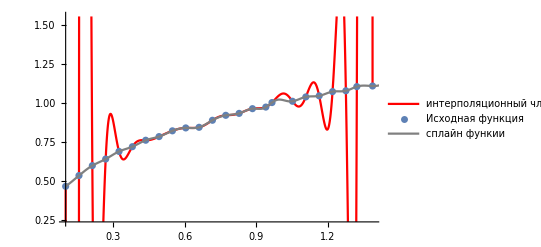

0.112

46.8393-1330.61 x+15650.3 x^2-102030. x^3+417208. x^4-1.13961×10^6 x^5+2.14983×10^6 x^6-2.84055×10^6 x^7+2.62283×10^6 x^8-1.65776×10^6 x^9+683316. x^10-165437. x^11+17839.3 x^12

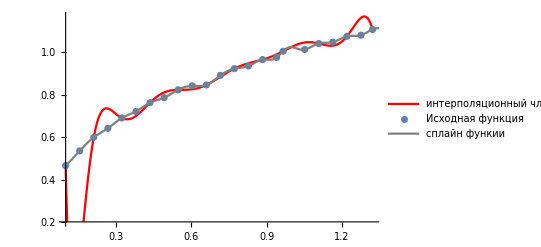

0.168

0.94212-11.3909 x+96.1663 x^2-367.025 x^3+778.261 x^4-968.7 x^5+703.047 x^6-275.121 x^7+44.8147 x^8

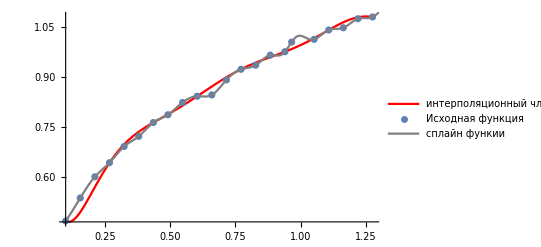

0.336

0.329401+1.52122 x-1.60157 x^2+0.996716 x^3-0.241883 x^4

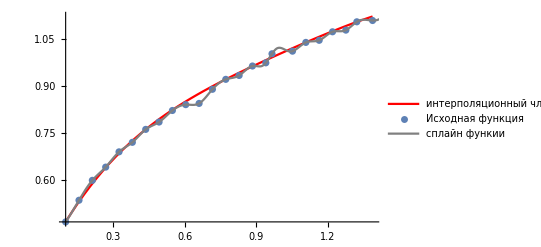

```mathematica
data = {{0.1, 0.46648}, {0.156, 0.53563}, {0.212, 0.599255}, {0.268, 0.641507}, {0.324, 0.690263}, {0.38, 0.720694}, {0.436, 0.76207}, {0.492, 0.785497}, {0.548, 0.822419}, {0.604, 0.841076}, {0.66, 0.845012}, {0.716, 0.890145}, {0.772, 0.921945}, {0.828, 0.934329}, {0.884, 0.964532}, {0.94, 0.974688}, {0.966, 1.00366}, {1.052, 1.01196}, {1.108, 1.03995}, {1.164, 1.04666}, {1.22, 1.07387}, {1.276, 1.07921}, {1.322, 1.10578}, {1.388, 1.10991}, {1.444, 1.13594}};

h=data[[2, 1]]-data[[1, 1]]
 inpl:=InterpolatingPolynomial[data, x]
Collect[inpl,x]

gr1:=Plot[inpl,{x,data[[1,1]],data[[24,1]]}, PlotStyle->Red, PlotLegends->{"интерполяционный член"}];
gr2:=ListPlot[data, PlotLegends->{"Исходная функция"}];
sp:=Interpolation[data, Method->"Spline"]
gr3:=Plot[{sp[x]},{x, 0.1, 1.444}, PlotStyle->Gray, PlotLegends->{"сплайн функии"}]

Show[{gr1, gr2, gr3}]


(*Для 12: *)
data2={};
For[i=1,i<=Length[data],i=i+2,
elem=data[[i]];
data2=Append[data2,elem]];

h=data2[[2, 1]]-data2[[1, 1]]
 inpl2:=InterpolatingPolynomial[data2, x]
Collect[inpl2,x]

gr1:=Plot[inpl2,{x,data[[1,1]],data[[23,1]]}, PlotStyle->Red, PlotLegends->{"интерполяционный член"}];
gr2:=ListPlot[data, PlotLegends->{"Исходная функция"}];
gr3:=Plot[{sp[x]},{x, 0.1, 1.444}, PlotStyle->Gray, PlotLegends->{"сплайн функии"}]

Show[{gr1, gr2, gr3}]

(*для n=8*)

(*data3={{0.1, 0.46648}};*)
data3={};
For[i=1,i<=Length[data],i=i+3,
elem3=data[[i]];
data3=Append[data3,elem3]];
h=data3[[2, 1]]-data3[[1, 1]]
 inpl3:=InterpolatingPolynomial[data3, x]
Collect[inpl3,x]
gr1:=Plot[inpl3,{x,data[[1,1]],data[[22,1]]}, PlotStyle->Red, PlotLegends->{"интерполяционный член"}];
gr2:=ListPlot[data, PlotLegends->{"Исходная функция"}];
gr3:=Plot[{sp[x]},{x, 0.1, 1.444}, PlotStyle->Gray, PlotLegends->{"сплайн функии"}]

Show[{gr1, gr2, gr3}]

(*для n=5*)
data4={};
For[i=1,i<=Length[data],i=i+6,
elem4=data[[i]];
data4=Append[data4,elem4]];
h=data4[[2, 1]]-data4[[1, 1]]
 inpl4:=InterpolatingPolynomial[data4, x]
Collect[inpl4,x]
gr1:=Plot[inpl4,{x,data[[1,1]],data[[24,1]]}, PlotStyle->Red, PlotLegends->{"интерполяционный член"}];
gr2:=ListPlot[data, PlotLegends->{"Исходная функция"}];
gr3:=Plot[{sp[x]},{x, 0.1, 1.444}, PlotStyle->Gray, PlotLegends->{"сплайн функии"}]

Show[{gr1, gr2, gr3}]
```